# How different Underbrush Build up and Cleanining Modalities affect a basic food chain

## Equations

```mathematica
Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt

Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt

Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et
```

Gt-dfG Gt-dG Gt+Gt (afG f+rG) (1-(Gt+aGR Rt)/KG)

Rt-dfR Rt-dR Rt+rR Rt (1-(aRE Et+aRG Gt+Rt)/KR)

Et-dE Et-dfE Et+(Et rE (1-(Et+aER Rt)/KE) (Et-xE))/KE

NOTE: The aRG, and aER are subtracted values in our equations in the paper. Although we added these two terms in the equations above, we made these two parameters negative to maintain consistency.

```mathematica
Simplify[Solve[{Gt1 == Gt, Rt1 == Rt, Et1 == Et}, {Gt, Rt, Et}]]
```

{{Gt→0,Rt→0,Et→(KE rE-√(rE (-4 dE KE^2-4 dfE KE^2+rE (KE-xE)^2))+rE xE)/(2 rE)},{Gt→0,Rt→0,Et→(KE rE+√(rE (-4 dE KE^2-4 dfE KE^2+rE (KE-xE)^2))+rE xE)/(2 rE)},{Gt→0,Rt→1/(2 (-1+aER aRE) rE rR)(2 dfR KR rE-aER aRE dfR KR rE+2 dR KR rE-aER aRE dR KR rE+aRE KE rE rR-2 KR rE rR+aER aRE KR rE rR+aRE rE rR xE-aER aRE^2 rE rR xE-aRE √(rE (-4 (1-aER aRE) rR (dE KE^2 rR+dfE KE^2 rR+rE (aER KR (dfR+dR-rR)+KE rR) xE)+rE (rR (KE+xE)+aER (dfR KR+dR KR-rR (KR+aRE xE)))^2))),Et→1/(2 (-1+aER aRE) rE rR)(-aER dfR KR rE-aER dR KR rE-KE rE rR+aER KR rE rR-rE rR xE+aER aRE rE rR xE+√(rE (-4 (1-aER aRE) rR (dE KE^2 rR+dfE KE^2 rR+rE (aER KR (dfR+dR-rR)+KE rR) xE)+rE (rR (KE+xE)+aER (dfR KR+dR KR-rR (KR+aRE xE)))^2)))},{Gt→0,Rt→1/(2 (-1+aER aRE) rE rR)(2 dfR KR rE-aER aRE dfR KR rE+2 dR KR rE-aER aRE dR KR rE+aRE KE rE rR-2 KR rE rR+aER aRE KR rE rR+aRE rE rR xE-aER aRE^2 rE rR xE+aRE √(rE (-4 (1-aER aRE) rR (dE KE^2 rR+dfE KE^2 rR+rE (aER KR (dfR+dR-rR)+KE rR) xE)+rE (rR (KE+xE)+aER (dfR KR+dR KR-rR (KR+aRE xE)))^2))),Et→-1/(2 (-1+aER aRE) rE rR)(aER dfR KR rE+aER dR KR rE+KE rE rR-aER KR rE rR+rE rR xE-aER aRE rE rR xE+√(rE (-4 (1-aER aRE) rR (dE KE^2 rR+dfE KE^2 rR+rE (aER KR (dfR+dR-rR)+KE rR) xE)+rE (rR (KE+xE)+aER (dfR KR+dR KR-rR (KR+aRE xE)))^2)))},{Gt→-((-2 afG aGR dfR f KR rE+aER afG aGR aRE dfR f KR rE+2 afG aGR^2 aRG dfR f KR rE-2 afG aGR dR f KR rE+aER afG aGR aRE dR f KR rE+2 afG aGR^2 aRG dR f KR rE-2 aGR dfR KR rE rG+aER aGR aRE dfR KR rE rG+2 aGR^2 aRG dfR KR rE rG-2 aGR dR KR rE rG+aER aGR aRE dR KR rE rG+2 aGR^2 aRG dR KR rE rG-afG aGR aRE f KE rE rR+afG aGR^2 aRE aRG f KE rE rR+2 dfG KG rE rR-2 aER aRE dfG KG rE rR-2 aGR aRG dfG KG rE rR+aER aGR aRE aRG dfG KG rE rR+2 dG KG rE rR-2 aER aRE dG KG rE rR-2 aGR aRG dG KG rE rR+aER aGR aRE aRG dG KG rE rR-2 afG f KG rE rR+2 aER afG aRE f KG rE rR+2 afG aGR aRG f KG rE rR-aER afG aGR aRE aRG f KG rE rR+2 afG aGR f KR rE rR-aER afG aGR aRE f KR rE rR-2 afG aGR^2 aRG f KR rE rR-aGR aRE KE rE rG rR+aGR^2 aRE aRG KE rE rG rR-2 KG rE rG rR+2 aER aRE KG rE rG rR+2 aGR aRG KG rE rG rR-aER aGR aRE aRG KG rE rG rR+2 aGR KR rE rG rR-aER aGR aRE KR rE rG rR-2 aGR^2 aRG KR rE rG rR-afG aGR aRE f rE rR xE+aER afG aGR aRE^2 f rE rR xE+afG aGR^2 aRE aRG f rE rR xE-aGR aRE rE rG rR xE+aER aGR aRE^2 rE rG rR xE+aGR^2 aRE aRG rE rG rR xE-aGR aRE √(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))/(2 (-1+aGR aRG) (-1+aER aRE+aGR aRG) rE (afG f+rG) rR)),Rt→(-2 afG dfR f KR rE+aER afG aRE dfR f KR rE+2 afG aGR aRG dfR f KR rE-2 afG dR f KR rE+aER afG aRE dR f KR rE+2 afG aGR aRG dR f KR rE-2 dfR KR rE rG+aER aRE dfR KR rE rG+2 aGR aRG dfR KR rE rG-2 dR KR rE rG+aER aRE dR KR rE rG+2 aGR aRG dR KR rE rG-afG aRE f KE rE rR+afG aGR aRE aRG f KE rE rR+2 aRG dfG KG rE rR-aER aRE aRG dfG KG rE rR-2 aGR aRG^2 dfG KG rE rR+2 aRG dG KG rE rR-aER aRE aRG dG KG rE rR-2 aGR aRG^2 dG KG rE rR-2 afG aRG f KG rE rR+aER afG aRE aRG f KG rE rR+2 afG aGR aRG^2 f KG rE rR+2 afG f KR rE rR-aER afG aRE f KR rE rR-2 afG aGR aRG f KR rE rR-aRE KE rE rG rR+aGR aRE aRG KE rE rG rR-2 aRG KG rE rG rR+aER aRE aRG KG rE rG rR+2 aGR aRG^2 KG rE rG rR+2 KR rE rG rR-aER aRE KR rE rG rR-2 aGR aRG KR rE rG rR-afG aRE f rE rR xE+aER afG aRE^2 f rE rR xE+afG aGR aRE aRG f rE rR xE-aRE rE rG rR xE+aER aRE^2 rE rG rR xE+aGR aRE aRG rE rG rR xE-aRE √(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))/(2 (-1+aGR aRG) (-1+aER aRE+aGR aRG) rE (afG f+rG) rR),Et→-1/(2 (-1+aER aRE+aGR aRG) rE (afG f+rG) rR)(aER afG dfR f KR rE+aER afG dR f KR rE+aER dfR KR rE rG+aER dR KR rE rG+afG f KE rE rR-afG aGR aRG f KE rE rR-aER aRG dfG KG rE rR-aER aRG dG KG rE rR+aER afG aRG f KG rE rR-aER afG f KR rE rR+KE rE rG rR-aGR aRG KE rE rG rR+aER aRG KG rE rG rR-aER KR rE rG rR+afG f rE rR xE-aER afG aRE f rE rR xE-afG aGR aRG f rE rR xE+rE rG rR xE-aER aRE rE rG rR xE-aGR aRG rE rG rR xE+√(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))},{Gt→-((-2 afG aGR dfR f KR rE+aER afG aGR aRE dfR f KR rE+2 afG aGR^2 aRG dfR f KR rE-2 afG aGR dR f KR rE+aER afG aGR aRE dR f KR rE+2 afG aGR^2 aRG dR f KR rE-2 aGR dfR KR rE rG+aER aGR aRE dfR KR rE rG+2 aGR^2 aRG dfR KR rE rG-2 aGR dR KR rE rG+aER aGR aRE dR KR rE rG+2 aGR^2 aRG dR KR rE rG-afG aGR aRE f KE rE rR+afG aGR^2 aRE aRG f KE rE rR+2 dfG KG rE rR-2 aER aRE dfG KG rE rR-2 aGR aRG dfG KG rE rR+aER aGR aRE aRG dfG KG rE rR+2 dG KG rE rR-2 aER aRE dG KG rE rR-2 aGR aRG dG KG rE rR+aER aGR aRE aRG dG KG rE rR-2 afG f KG rE rR+2 aER afG aRE f KG rE rR+2 afG aGR aRG f KG rE rR-aER afG aGR aRE aRG f KG rE rR+2 afG aGR f KR rE rR-aER afG aGR aRE f KR rE rR-2 afG aGR^2 aRG f KR rE rR-aGR aRE KE rE rG rR+aGR^2 aRE aRG KE rE rG rR-2 KG rE rG rR+2 aER aRE KG rE rG rR+2 aGR aRG KG rE rG rR-aER aGR aRE aRG KG rE rG rR+2 aGR KR rE rG rR-aER aGR aRE KR rE rG rR-2 aGR^2 aRG KR rE rG rR-afG aGR aRE f rE rR xE+aER afG aGR aRE^2 f rE rR xE+afG aGR^2 aRE aRG f rE rR xE-aGR aRE rE rG rR xE+aER aGR aRE^2 rE rG rR xE+aGR^2 aRE aRG rE rG rR xE+aGR aRE √(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))/(2 (-1+aGR aRG) (-1+aER aRE+aGR aRG) rE (afG f+rG) rR)),Rt→(-2 afG dfR f KR rE+aER afG aRE dfR f KR rE+2 afG aGR aRG dfR f KR rE-2 afG dR f KR rE+aER afG aRE dR f KR rE+2 afG aGR aRG dR f KR rE-2 dfR KR rE rG+aER aRE dfR KR rE rG+2 aGR aRG dfR KR rE rG-2 dR KR rE rG+aER aRE dR KR rE rG+2 aGR aRG dR KR rE rG-afG aRE f KE rE rR+afG aGR aRE aRG f KE rE rR+2 aRG dfG KG rE rR-aER aRE aRG dfG KG rE rR-2 aGR aRG^2 dfG KG rE rR+2 aRG dG KG rE rR-aER aRE aRG dG KG rE rR-2 aGR aRG^2 dG KG rE rR-2 afG aRG f KG rE rR+aER afG aRE aRG f KG rE rR+2 afG aGR aRG^2 f KG rE rR+2 afG f KR rE rR-aER afG aRE f KR rE rR-2 afG aGR aRG f KR rE rR-aRE KE rE rG rR+aGR aRE aRG KE rE rG rR-2 aRG KG rE rG rR+aER aRE aRG KG rE rG rR+2 aGR aRG^2 KG rE rG rR+2 KR rE rG rR-aER aRE KR rE rG rR-2 aGR aRG KR rE rG rR-afG aRE f rE rR xE+aER afG aRE^2 f rE rR xE+afG aGR aRE aRG f rE rR xE-aRE rE rG rR xE+aER aRE^2 rE rG rR xE+aGR aRE aRG rE rG rR xE+aRE √(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))/(2 (-1+aGR aRG) (-1+aER aRE+aGR aRG) rE (afG f+rG) rR),Et→1/(2 (-1+aER aRE+aGR aRG) rE (afG f+rG) rR)(-aER afG dfR f KR rE-aER afG dR f KR rE-aER dfR KR rE rG-aER dR KR rE rG-afG f KE rE rR+afG aGR aRG f KE rE rR+aER aRG dfG KG rE rR+aER aRG dG KG rE rR-aER afG aRG f KG rE rR+aER afG f KR rE rR-KE rE rG rR+aGR aRG KE rE rG rR-aER aRG KG rE rG rR+aER KR rE rG rR-afG f rE rR xE+aER afG aRE f rE rR xE+afG aGR aRG f rE rR xE-rE rG rR xE+aER aRE rE rG rR xE+aGR aRG rE rG rR xE+√(rE (4 (-1+aER aRE+aGR aRG) (afG f+rG) rR ((1-aGR aRG) dE KE^2 rG rR+dfE KE^2 rG rR-aGR aRG dfE KE^2 rG rR+aER dfR KR rE rG xE+aER dR KR rE rG xE-aER aRG dfG KG rE rR xE-aER aRG dG KG rE rR xE+KE rE rG rR xE-aGR aRG KE rE rG rR xE+aER aRG KG rE rG rR xE-aER KR rE rG rR xE+afG f ((1-aGR aRG) dE KE^2 rR+(1-aGR aRG) dfE KE^2 rR+rE ((1-aGR aRG) KE rR+aER (dfR KR+dR KR+aRG KG rR-KR rR)) xE))+rE ((-1+aGR aRG) (afG f+rG) rR (KE+xE)+aER (-dfR KR rG-dR KR rG+aRG dfG KG rR+aRG dG KG rR-aRG KG rG rR+KR rG rR+aRE rG rR xE-afG f (dfR KR+dR KR+aRG KG rR-KR rR-aRE rR xE)))^2)))},{Gt→0,Rt→-(KR (dfR+dR-rR))/rR,Et→0},{Gt→(-aGR KR rG (dfR+dR-rR)+KG (dfG+dG-rG) rR-afG f (aGR KR (dfR+dR-rR)+KG rR))/((-1+aGR aRG) (afG f+rG) rR),Rt→(dfR KR rG+dR KR rG-aRG dfG KG rR-aRG dG KG rR+aRG KG rG rR-KR rG rR+afG f (dfR KR+dR KR+aRG KG rR-KR rR))/((-1+aGR aRG) (afG f+rG) rR),Et→0},{Gt→-(KG (dfG+dG-afG f-rG))/(afG f+rG),Rt→0,Et→(KE rE-√(rE (-4 dE KE^2-4 dfE KE^2+rE (KE-xE)^2))+rE xE)/(2 rE)},{Gt→-(KG (dfG+dG-afG f-rG))/(afG f+rG),Rt→0,Et→(KE rE+√(rE (-4 dE KE^2-4 dfE KE^2+rE (KE-xE)^2))+rE xE)/(2 rE)},{Gt→0,Rt→0,Et→0},{Gt→(KG (-dfG-dG+afG f+rG))/(afG f+rG),Rt→0,Et→0}}

Forest Fire Regimes

### Slope = Rate of underbrush build up = Probability of Fire Occurring Mod[y,z] where z is how frequently underbrush is cleared through controlled burn or other means

## Linear Regimes

### z = 30 steps w/ variable slope

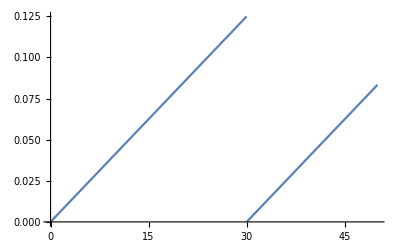

```mathematica
lin125s30[y_] := Mod[y, 30]/240;
Plot[lin125s30[y], {y, 0, 50}]
```

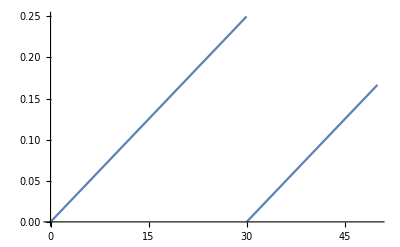

```mathematica
lin25s30[y_] := Mod[y, 30]/120;
Plot[lin25s30[y], {y, 0, 50}]
```

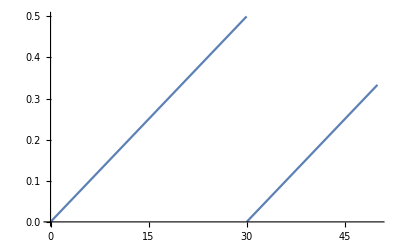

```mathematica
lin50s30[y_] := Mod[y, 30]/60;
Plot[lin50s30[y], {y, 0, 50}]
```

### z = 15 steps w/ variable slope

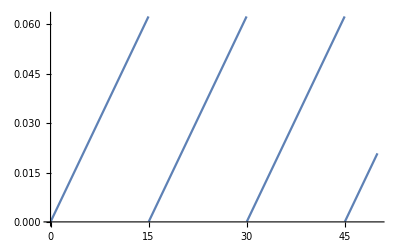

```mathematica
lin125s15[y_] := Mod[y, 15]/240;
Plot[lin125s15[y], {y, 0, 50}]
```

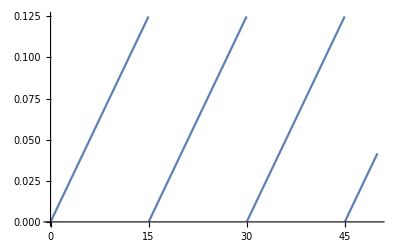

```mathematica
lin25s15[y_] := Mod[y, 15]/120;
Plot[lin25s15[y], {y, 0, 50}]
```

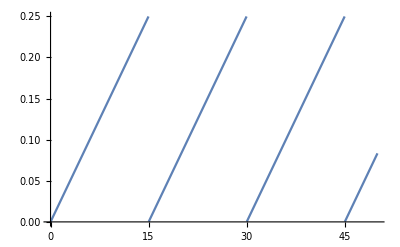

```mathematica
lin50s15[y_] := Mod[y, 15]/60;
Plot[lin50s15[y], {y, 0, 50}]
```

### z = 5 steps w/ variable slope

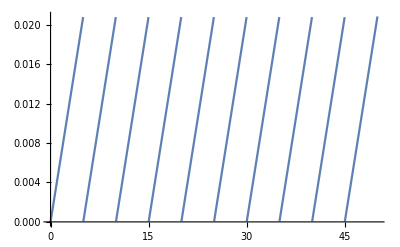

```mathematica
lin125s5[y_] := Mod[y, 5]/240;
Plot[lin125s5[y], {y, 0, 50}]
```

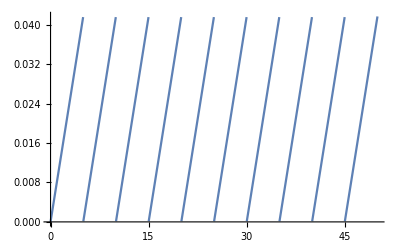

```mathematica
lin25s5[y_] := Mod[y, 5]/120;
Plot[lin25s5[y], {y, 0, 50}]
```

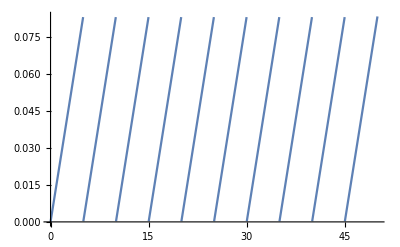

```mathematica
lin50s5[y_] := Mod[y, 5]/60;
Plot[lin50s5[y], {y, 0, 50}]
```

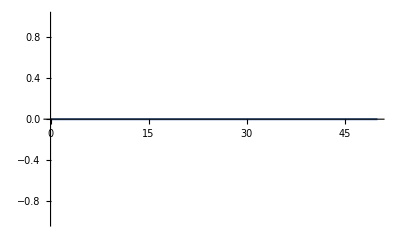

```mathematica
zero[y_] := 0;
Plot[zero[y], {y, 0, 50}]
```

### Probing ~1/240 slope polynomial and square root analogs

```mathematica
lin125s5[y_] := Mod[y, 5]/240;
Plot[lin125s5[y], {y, 0, 50}]
```

-Graphics-

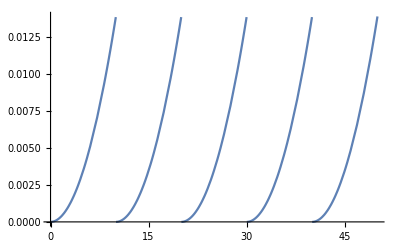

```mathematica
sq125s10[y_] := (Mod[y,10]/84.84)^2;
Plot[sq125s10[y], {y, 0, 50}]
```

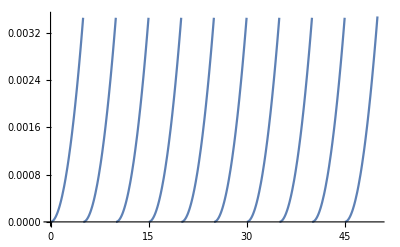

```mathematica
sq125s5[y_] := (Mod[y,5]/84.84)^2;
Plot[sq125s5[y], {y, 0, 50}]
```

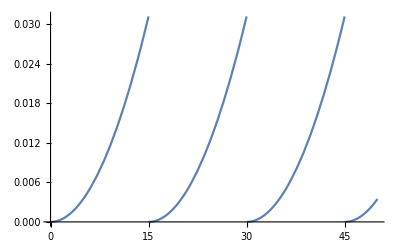

```mathematica
sq125s15[y_] := (Mod[y,15]/84.84)^2;
Plot[sq125s15[y], {y, 0, 50}]
```

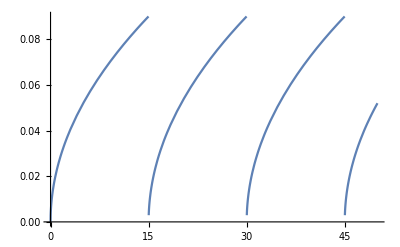

```mathematica
sqrt125s15[y_] := Sqrt[Mod[y,15]]/43;
Plot[sqrt125s15[y], {y, 0, 50}]
```

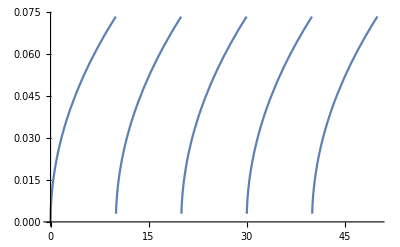

```mathematica
sqrt125s10[y_] := Sqrt[Mod[y,10]]/43;
Plot[sqrt125s10[y], {y, 0, 50}]
```

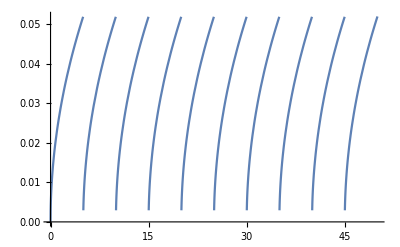

```mathematica
sqrt125s5[y_] := Sqrt[Mod[y,5]]/43;
Plot[sqrt125s5[y], {y, 0, 50}]
```

Stochastic Model with treatments

### Setting up parameters

```mathematica
(*Notes:
- f = 1 when random number is below that of current value in fire distribution (t = 0)
- dfPopulation will have magnitude only when fire distribution is @ t = 0 
- G is square foot of grass; context is 100 acres of land which is 4.356e6 sq ft of grass

*)

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;

Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;

Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;


KG = 4356000;
KR = 4000;
KE = 200;

rG = .4;
rR = .3;
rE = .4;
afG = .1;

dG = .25;
dR = .1;
dE = .09;

xE = 20;

dfG = 0; (*initialize 0*)
dfR = 0;
dfE = 0;
f = 0;

aGR = 500;
aRG = -.00133; (*.00266?*)
aRE = 25;
aER = -.02;
```

### Equilibrium with Parameters

```mathematica
Solve[{Gt1 == Gt, Rt1 == Rt, Et1 == Et}, {Gt, Rt, Et}]
```

{{Gt→757793.,Rt→1751.41,Et→76.9247},{Gt→0.,Rt→305.556+535.038 ⅈ,Et→94.4444-21.4015 ⅈ},{Gt→0.,Rt→305.556-535.038 ⅈ,Et→94.4444+21.4015 ⅈ},{Gt→0.,Rt→0.,Et→110.-30. ⅈ},{Gt→1.6335×10^6,Rt→0.,Et→110.-30. ⅈ},{Gt→0.,Rt→0.,Et→110.+30. ⅈ},{Gt→1.6335×10^6,Rt→0.,Et→110.+30. ⅈ},{Gt→1.24327×10^6,Rt→780.463,Et→141.59},{Gt→0.,Rt→2666.67,Et→-4.73695×10^-15},{Gt→180280.,Rt→2906.44,Et→2.65508×10^-15},{Gt→1.6335×10^6,Rt→0.,Et→0.},{Gt→0.,Rt→0.,Et→0.}}

### Control (No Fires)

0

141.59

12432.7

780.464

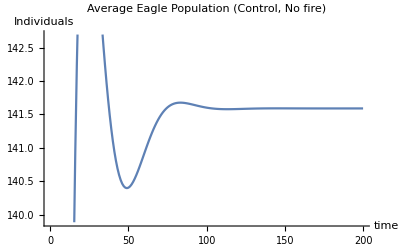

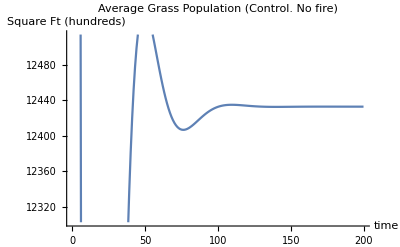

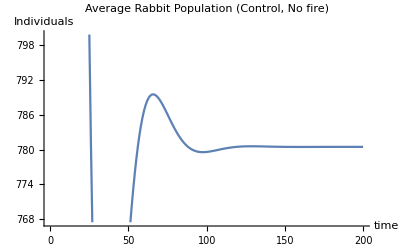

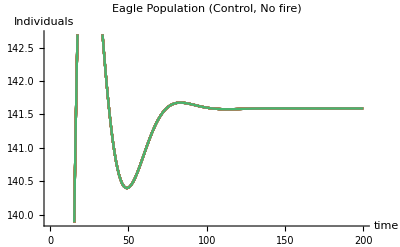

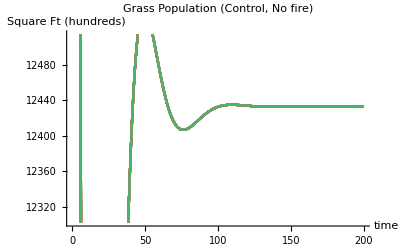

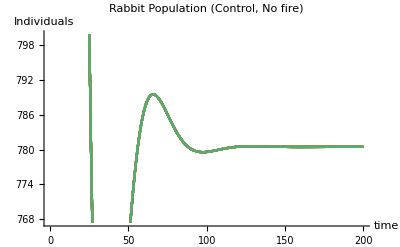

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt/100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[zero[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30


Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]


plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (Control, No fire)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (Control. No fire)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (Control, No fire)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (Control, No fire)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (Control, No fire)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (Control, No fire)", AxesLabel -> {"time", "Individuals"}]
```

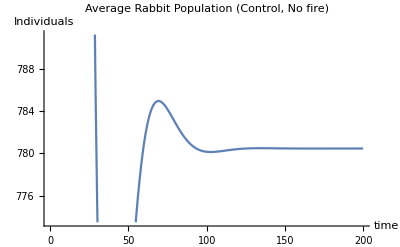

-Graphics-

### Linear Regimes

#### 30 time steps

1/60 slope

623/30

{100,102.2,104.425,105.495,107.092,109.699,111.118,112.566,112.86,114.353,113.905,113.333,112.139,110.955,110.756,109.563,108.267,105.888,104.607,104.149,101.912,101.172,99.5595,97.7979,96.2667,95.2442,93.4208,92.9706,89.9505,89.1087,86.4368,85.078,81.7549,80.3714,77.7311,75.5989,74.2043,72.7018,71.3981,69.2677,66.5462,65.1369,63.1277,60.6956,58.2331,56.8687,55.1616,51.7909,49.4143,48.1624,46.0145,44.7412,43.0065,41.5063,39.56,37.407,35.3166,33.7079,31.6822,30.1517,28.4696,27.3201,26.0244,24.4586,22.96,21.8907,20.413,19.2521,18.2212,17.2086,16.0533,15.23,13.9177,12.9612,12.1944,11.3581,10.7175,10.0491,8.92062,8.3359,7.87718,7.43883,6.66808,5.99543,5.61232,5.22038,4.8907,4.21566,3.93178,3.65948,3.4035,3.16229,2.6374,2.41975,2.20882,2.01898,1.73481,1.5725,1.41217,1.27585,1.14844,1.03052,0.922281,0.802782,0.714116,0.548239,0.482658,0.423334,0.36943,0.322331,0.281301,0.244462,0.212009,0.173331,0.139963,0.121088,0.10483,0.0904965,0.0781739,0.0648296,0.0476678,0.0412238,0.0355061,0.0299262,0.0258586,0.022266,0.0190361,0.0164154,0.014107,0.0121397,0.0097192,0.00838505,0.00708225,0.00611536,0.00527261,0.00453458,0.00390408,0.00336181,0.00289163,0.00248741,0.00213863,0.00182748,0.00150108,0.00129159,0.00110121,0.000947028,0.000705571,0.000608661,0.00052378,0.000451084,0.000387203,0.000332532,0.000284721,0.000244787,0.000210396,0.00018087,0.000155412,0.000133461,0.000114208,0.0000980647,0.0000752072,0.000064663,0.0000556109,0.0000457955,0.0000394668,0.0000340057,0.0000291197,0.0000237193,0.0000200097,0.0000164135,0.0000141761,0.0000122333,0.0000105401,8.72355×10^-6,7.52839×10^-6,6.49319×10^-6,4.99392×10^-6,4.31699×10^-6,3.72831×10^-6,3.21359×10^-6,2.53132×10^-6,2.14457×10^-6,1.85317×10^-6,1.59348×10^-6,1.37303×10^-6,1.18468×10^-6,1.02186×10^-6,8.80964×10^-7,7.57272×10^-7,5.86199×10^-7,4.89665×10^-7,4.22279×10^-7,3.64248×10^-7,3.12304×10^-7,2.34016×10^-7,2.0213×10^-7,1.74461×10^-7,1.49792×10^-7,1.2899×10^-7,1.11221×10^-7}

{20000,17573.4,15496.3,12769.8,11428.9,10890.7,10081.1,9617.88,8804.76,8713.79,8338.48,7910.38,7400.86,7335.92,7496.17,7481.81,7426.05,7172.83,7253.97,7567.88,7336.71,7675.09,7643.56,7501.13,7616.88,7763.7,7759.73,8148.49,7589.45,7916.62,7761.69,7734.43,7287.71,7375.9,6877.83,6883.87,7112.82,7159.19,7429.11,7136.66,6908.2,7163.75,7072.55,6599.66,6305.53,6505.02,6642.28,6393.96,6244.71,6625.11,6561.19,6835.86,6759.68,6667.34,6067.94,5701.15,5498.07,5537.17,5171.17,5128.43,5173.76,5387.95,5426.27,5421.18,5177.52,5243.87,5050.76,4873.54,4754.17,4681.64,4499.47,4588.66,4334.54,4217.95,4183.62,3867.9,3865.19,3704.14,3366.81,3151.97,3257.45,3280.04,3223.51,3055.57,3030.74,2887.44,2901.55,2906.53,2930.72,2799.01,2771.23,2772.1,2507.97,2471.8,2283.83,2252.42,2083.23,2037.17,2046.56,2109.43,2137.63,2152.78,2169.37,2048.01,2079.48,2060.58,1931.87,1859.13,1781.07,1742.87,1779.09,1675.34,1681.3,1642.99,1563.09,1567.04,1568.47,1486.02,1389.95,1366.92,1415.61,1420.85,1297.77,1248.28,1323.32,1307.52,1266.64,1330.88,1312.43,1322.47,1290.41,1300.35,1194.69,1209.15,1219.41,1178.75,1142.19,1122.14,1124.21,1173.34,1126.22,1144.56,1094.56,1134.79,1067.6,1122.35,1107.35,1112.12,1112.56,1143.68,1119.44,1101.4,1134.43,1167.81,1146.,1205.17,1234.67,1237.54,1152.97,1148.54,1056.48,1093.53,1088.72,1064.74,1041.28,1100.82,1094.95,1087.43,1127.66,1113.65,1148.66,1133.23,1055.47,1009.74,1051.61,1044.33,1054.52,1097.4,1115.34,1129.09,1079.07,1072.67,1034.19,1006.3,987.628,1028.59,1057.34,1074.49,1082.21,1034.53,1027.55,1040.91,1024.69,916.615,940.095,985.865,997.572,1016.09,1021.01,1066.75}

{2000,2124.,2140.62,2012.84,1882.78,1824.84,1698.77,1587.91,1403.04,1326.05,1201.11,1095.36,977.503,916.062,881.421,845.025,798.209,745.44,717.801,722.489,666.226,675.115,664.902,657.663,659.405,656.342,654.58,689.145,643.904,671.352,674.137,692.87,687.55,699.294,690.821,707.786,748.697,772.576,828.341,850.295,877.426,932.844,934.168,869.29,905.255,919.158,967.302,958.481,952.884,1046.48,1082.02,1166.22,1194.32,1270.58,1248.63,1288.95,1319.79,1371.88,1368.82,1362.48,1417.39,1533.69,1596.21,1700.39,1691.49,1731.99,1791.5,1787.91,1838.99,1837.59,1899.25,2020.33,1963.53,2008.91,2047.38,2017.04,2071.2,2088.9,2067.27,2009.54,2127.86,2177.13,2189.66,2145.03,2088.16,2068.07,2135.74,2239.97,2263.06,2198.73,2221.82,2278.61,2195.72,2192.65,2092.03,2072.08,1921.7,1882.21,1922.72,1981.98,2045.77,2084.27,2165.48,2164.45,2237.62,2306.51,2230.73,2181.89,2129.79,2094.,2169.39,2101.13,2124.76,2136.34,2208.4,2237.07,2218.4,2087.72,2023.57,2020.28,2083.43,2098.45,1921.5,1912.57,2029.79,2072.62,2006.92,2124.86,2105.46,2122.44,2158.8,2149.1,2052.76,2119.2,2109.08,2029.79,1981.45,1971.9,1964.42,2052.51,1970.34,2013.37,1987.36,2064.46,1931.65,2018.24,1979.72,1996.44,2003.49,2074.34,2014.69,1956.15,1984.99,1994.6,1972.23,2084.88,2158.82,2179.34,2090.46,2068.07,2032.01,2101.18,2065.59,2036.69,1966.28,2079.31,2026.99,2039.29,2126.28,2087.29,2126.43,2082.13,2010.34,1946.71,1980.54,1989.62,2004.32,2074.4,2108.45,2137.39,2097.77,2100.66,1989.64,1984.94,1948.2,2029.8,2113.34,2179.87,2157.99,2091.26,2099.38,2094.13,2045.58,1898.16,1915.85,1997.2,2024.23,2062.07,2027.28,2101.3}

1.11221×10^-7

1066.75

2101.3

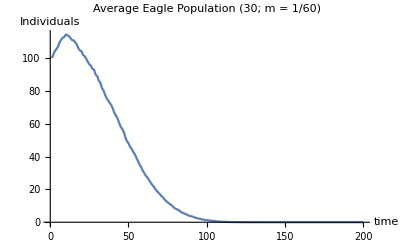

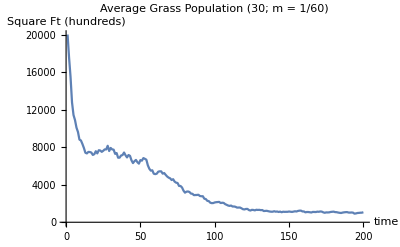

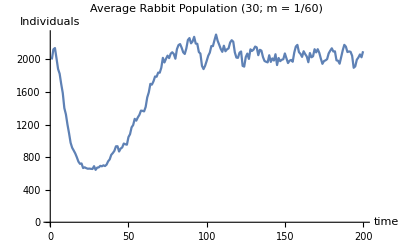

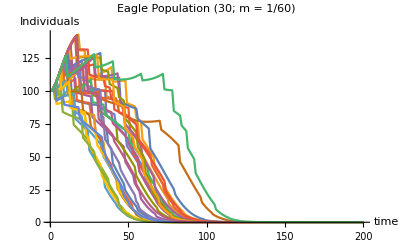

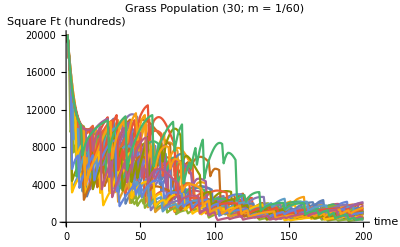

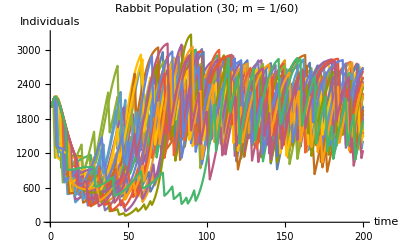

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt/100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin50s30[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30


Eaverage = Total[compiledE, {1}]/30
Gaverage = Total[compiledG,{1}]/30
Raverage = Total[compiledR,{1}]/30


avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (30; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (30; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (30; m = 1/60)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (30; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (30; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (30; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
```

1/120 slope

85/6

0.0138749

1208.37

2302.86

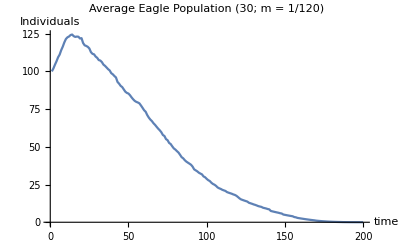

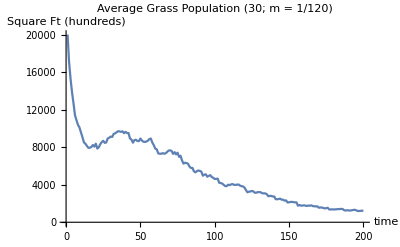

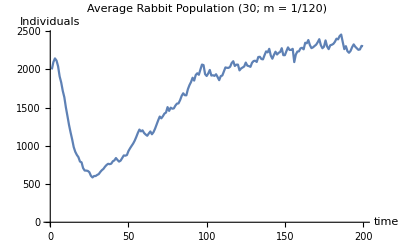

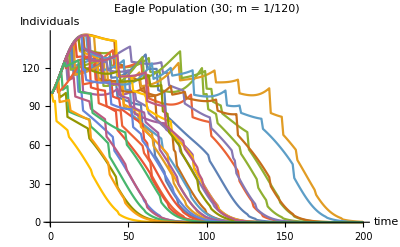

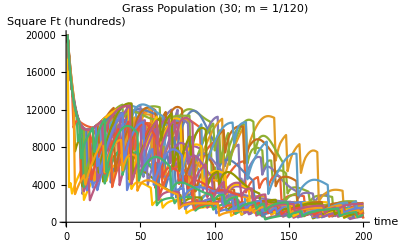

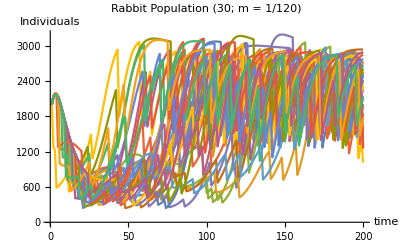

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt / 100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin25s30[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (30; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (30; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (30; m = 1/120)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (30; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (30; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (30; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
```

slope 1/240

43/5

48.3706

5440.84

1832.16

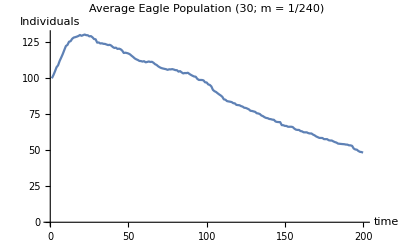

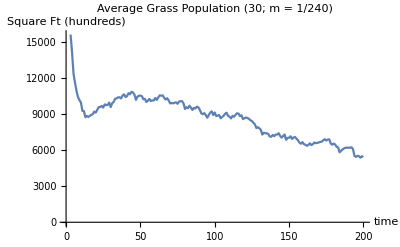

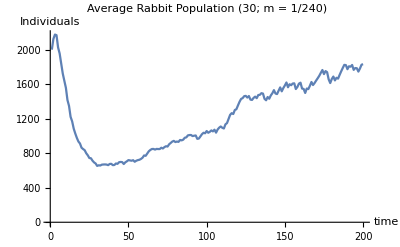

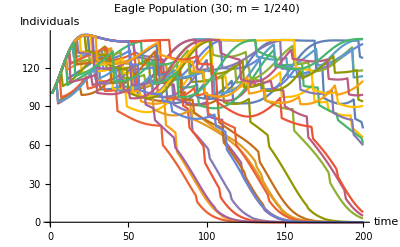

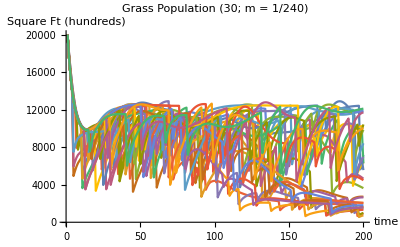

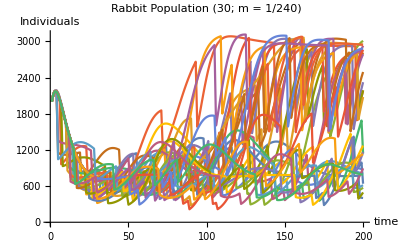

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin125s30[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (30; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (30; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (30; m = 1/240)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (30; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (30; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (30; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
```

#### 15 steps before clearing underbrush

1/60 slope

563/30

0.0000386946

1069.67

2070.32

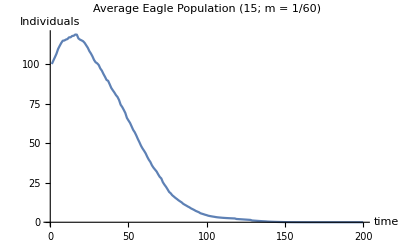

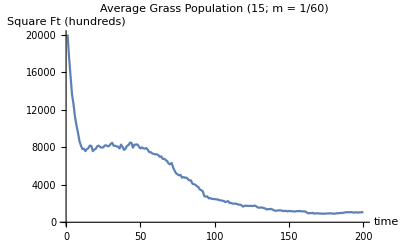

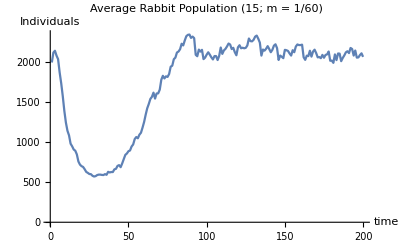

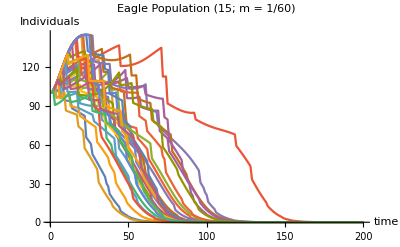

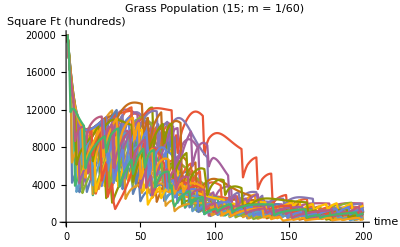

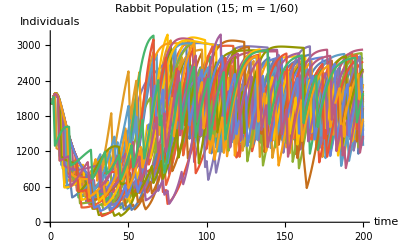

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin50s15[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (15; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (15; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (15; m = 1/60)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (15; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (15; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (15; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
```

1/120 slope

152/15

22.2539

3623.52

2262.18

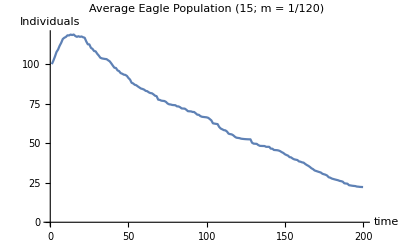

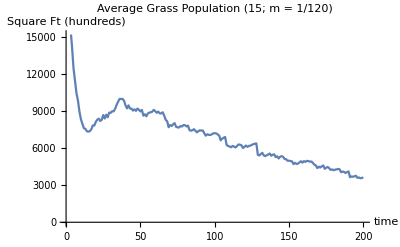

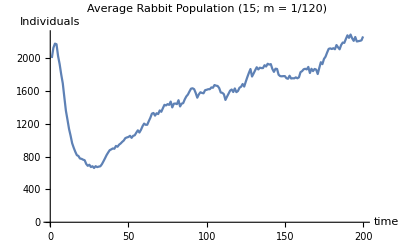

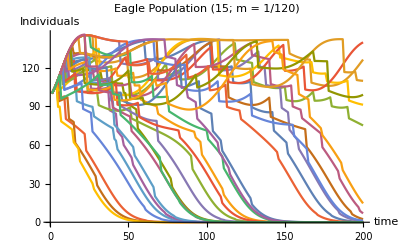

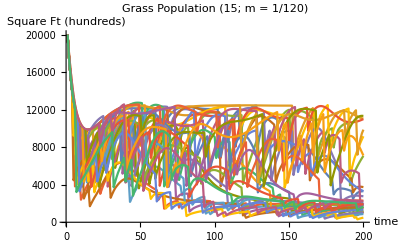

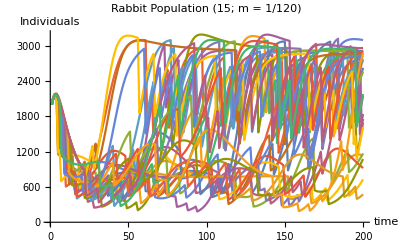

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin25s15[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (15; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (15; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (15; m = 1/120)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (15; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (15; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (15; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
```

1/240 slope

179/30

81.9983

7888.75

1404.72

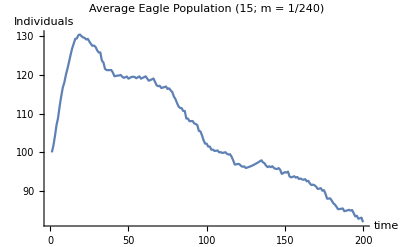

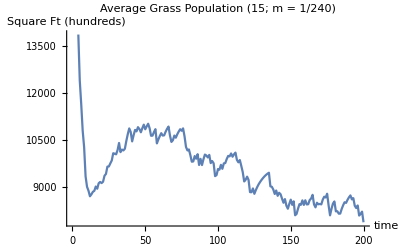

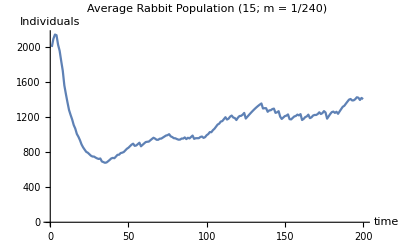

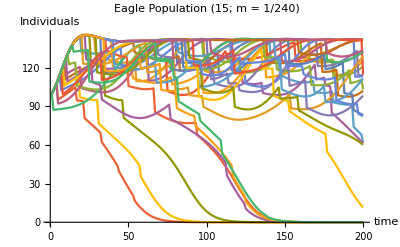

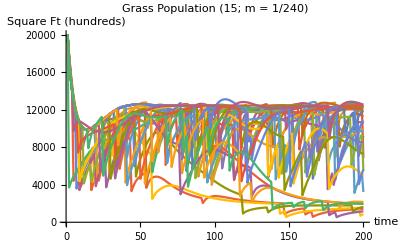

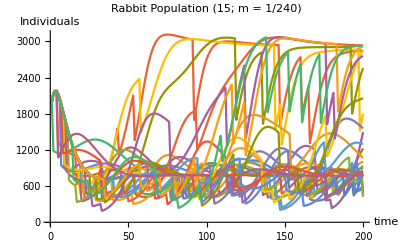

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin125s15[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (15; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (15; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (15; m = 1/240)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (15; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (15; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (15; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
```

#### 5 time steps before brush clearing

1/60 slope

106/15

59.1849

6198.67

1716.31

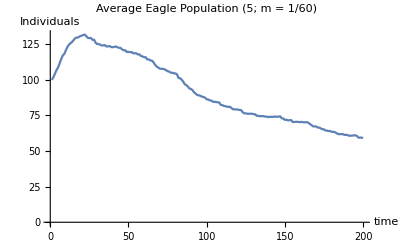

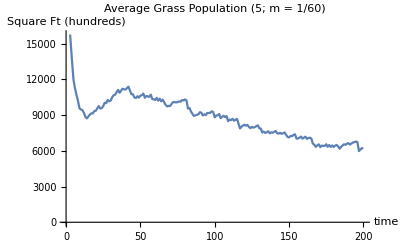

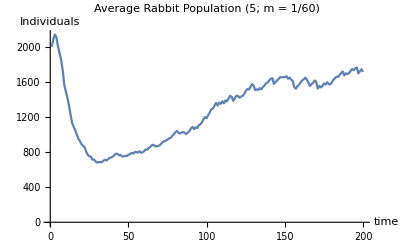

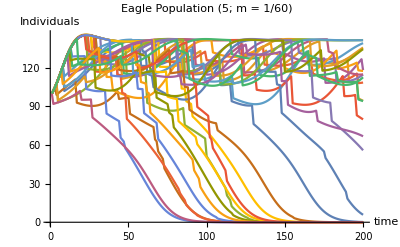

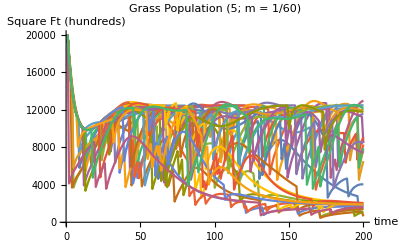

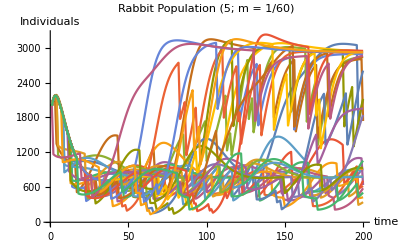

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin50s5[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;
	
(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (5; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (5; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (5; m = 1/60)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (5; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (5; m = 1/60)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (5; m = 1/60)", AxesLabel -> {"time", "Individuals"}]
```

1/120 slope

97/30

120.244

10818.6

986.468

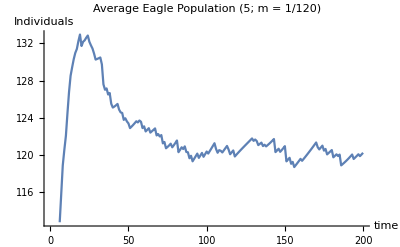

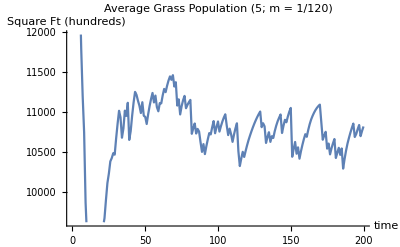

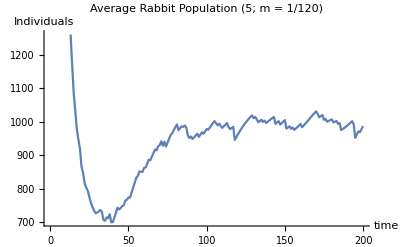

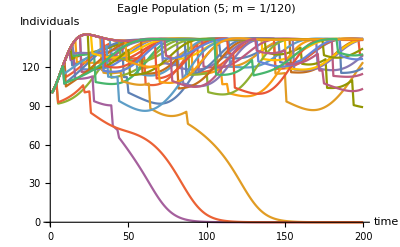

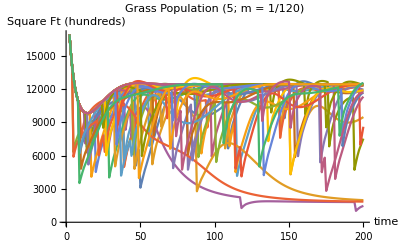

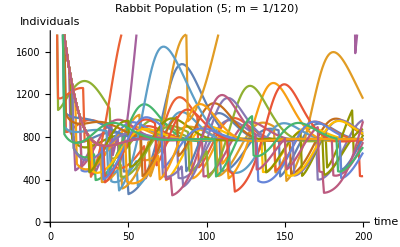

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin25s5[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (5; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (5; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (5; m = 1/120)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (5; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (5; m = 1/120)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (5; m = 1/120)", AxesLabel -> {"time", "Individuals"}]
```

1/240 slope

53/30

132.977

11832.8

848.277

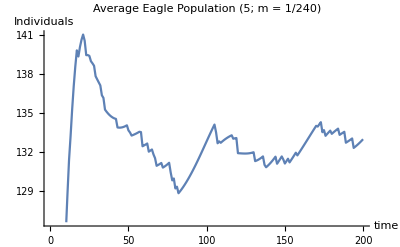

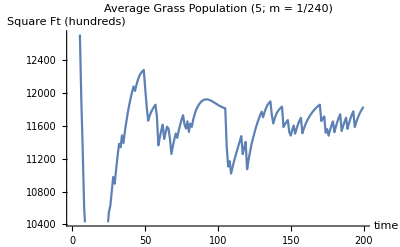

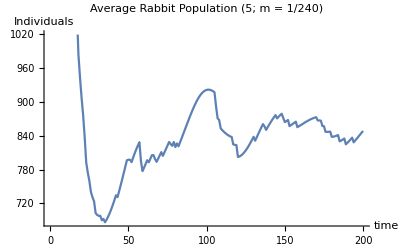

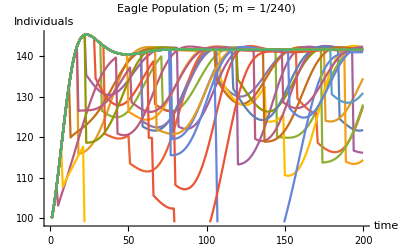

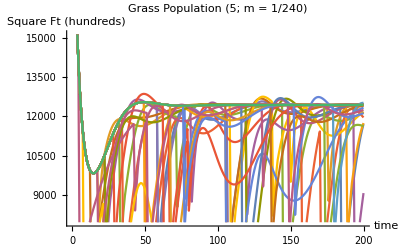

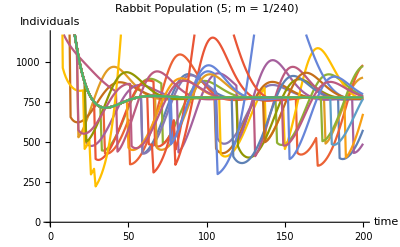

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[lin125s5[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (5; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (5; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (5; m = 1/240)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (5; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (5; m = 1/240)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (5; m = 1/240)", AxesLabel -> {"time", "Individuals"}]
```

### Probing the 1/240 slope analogs - polynomials

#### 5 steps; x^2/84.84 ~ slope 1/240

1/10

141.586

12433.2

780.277

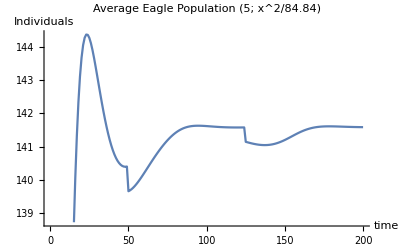

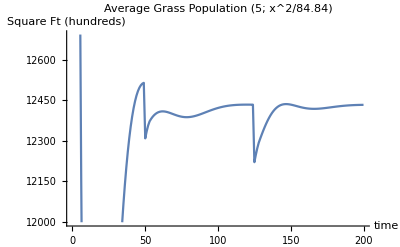

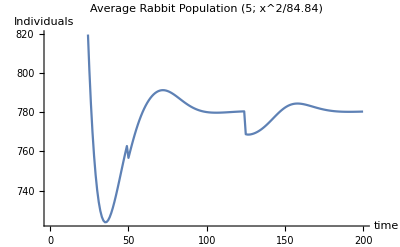

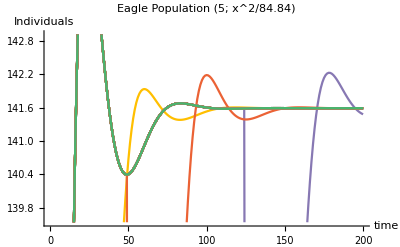

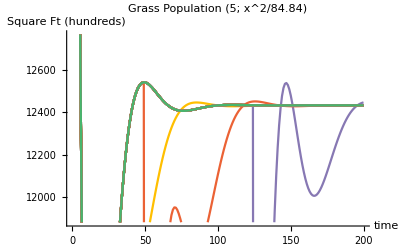

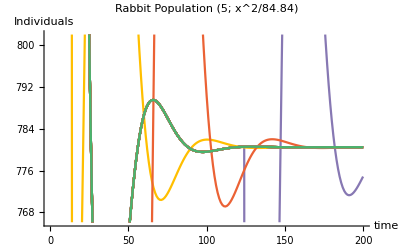

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sq125s5[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (5; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (5; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (5; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (5; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (5; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (5; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
```

#### 10 steps; x^2/84.84 ~ slope 1/240

3/5

138.363

12276.7

774.37

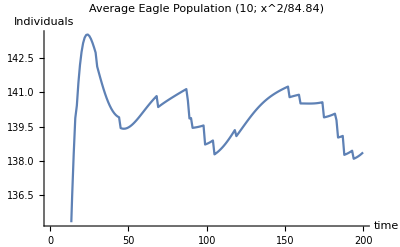

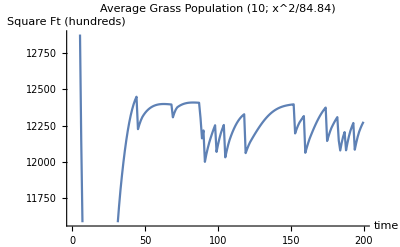

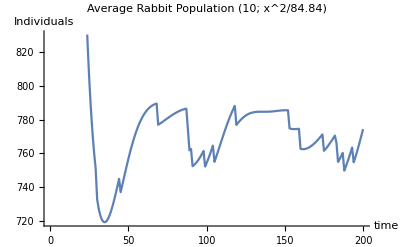

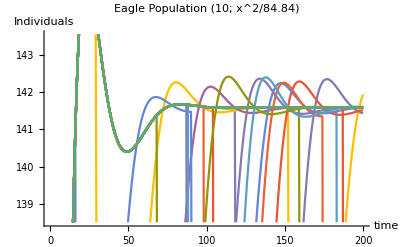

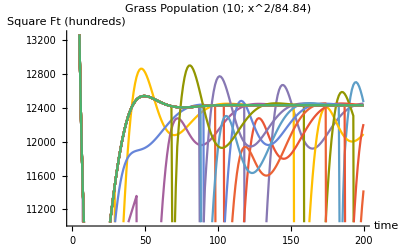

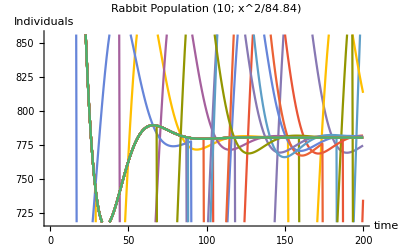

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sq125s10[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (10; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (10; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (10; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (10; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (10; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (10; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
```

#### 15 steps; x^2/84.84 ~ slope 1/240

17/10

134.541

11685.5

780.756

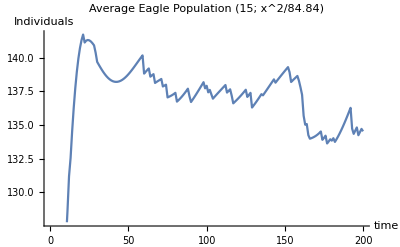

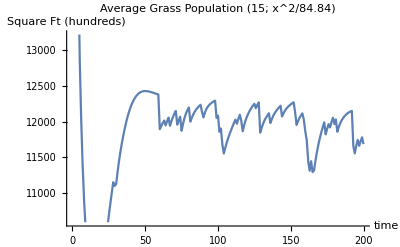

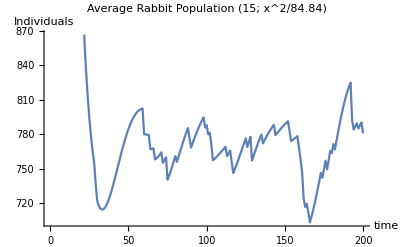

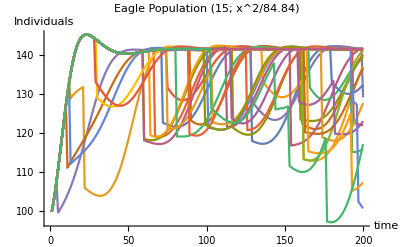

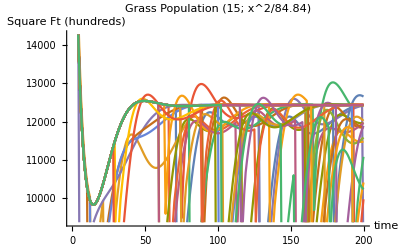

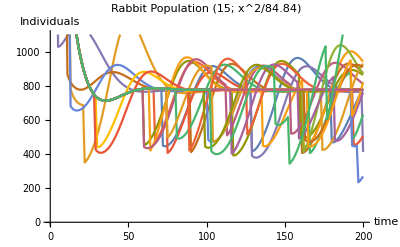

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sq125s15[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (15; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (15; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (15; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (15; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (15; x^2/84.84)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (15; x^2/84.84)", AxesLabel -> {"time", "Individuals"}]
```

### Probing the 1/240 slope analogs - square roots

158/15

13.3122

2899.33

2187.05

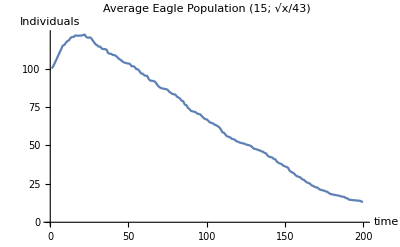

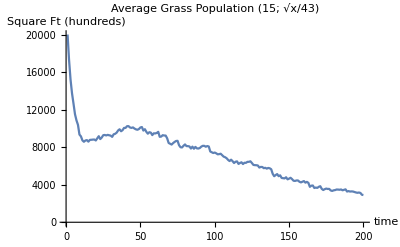

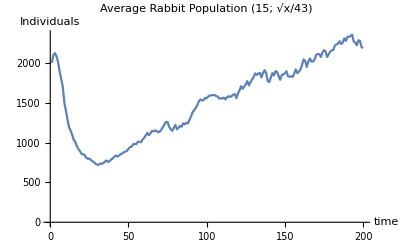

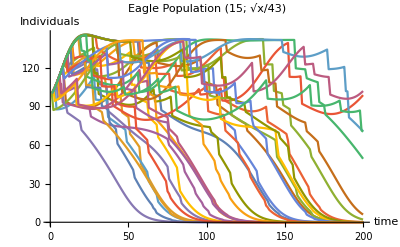

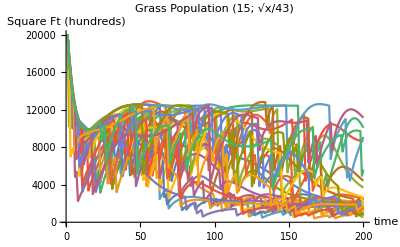

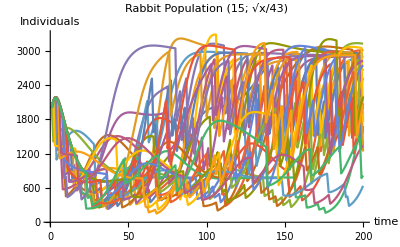

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sqrt125s15[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (15; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (15; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (15; √x/43)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (15; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (15; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (15; √x/43)", AxesLabel -> {"time", "Individuals"}]
```

83/10

33.4423

4470.51

2046.57

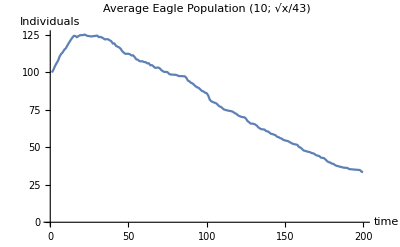

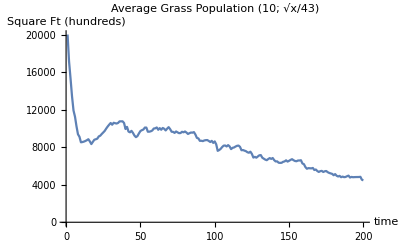

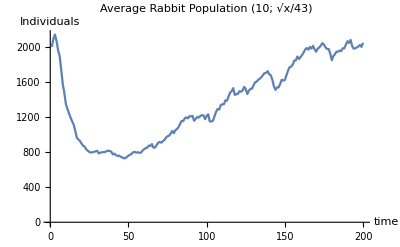

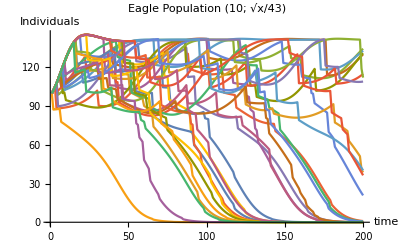

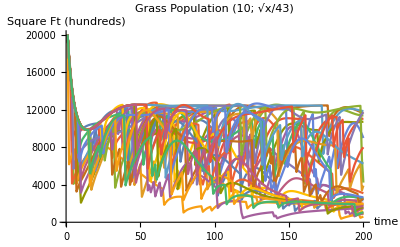

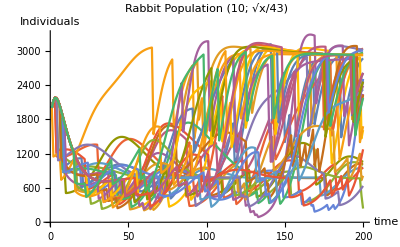

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sqrt125s10[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];


Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;

(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (10; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (10; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (10; √x/43)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (10; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (10; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (10; √x/43)", AxesLabel -> {"time", "Individuals"}]
```

17/3

73.2509

7482.06

1564.07

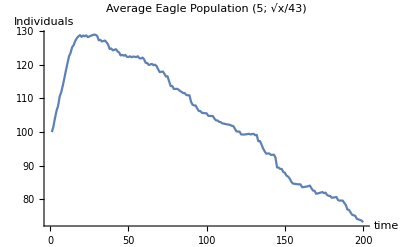

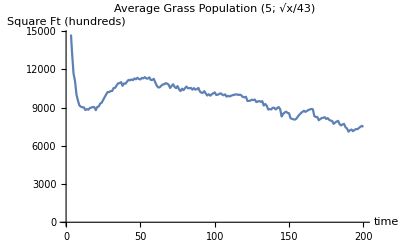

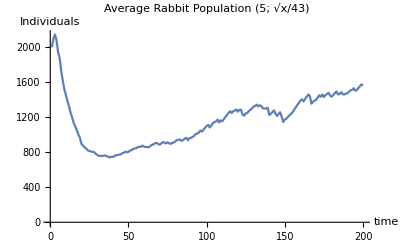

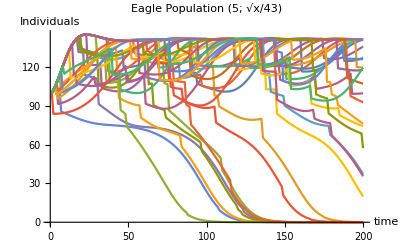

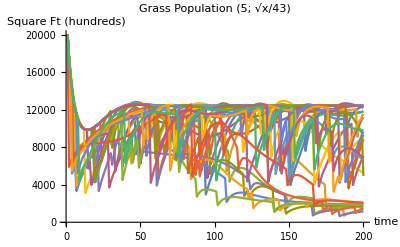

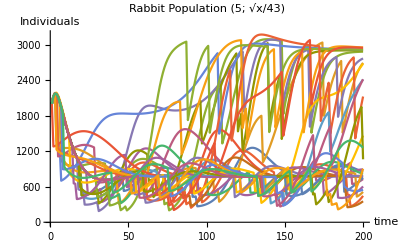

```mathematica
numruns = 30; 
j = 200;
compiledG = Table[0, {count, numruns}, {i, j}];
compiledR = Table[0, {count, numruns}, {i, j}];
compiledE = Table[0, {count, numruns}, {i, j}];
tabnof = Table[0, {i, numruns}];

Do[
(*lin 25 fire distribution*)
x = i; (*x is the adjustable time analog to i*)
(*set up initial populations and tables*)
Gt = 2000000;
Rt = 2000;
Et = 100;

tableG = Table[0,{i,j}];
tableR = Table[0,{i,j}];
tableE = Table[0,{i,j}];


nof = 0; (*number of fires counter*)

Do[

compiledG[[count,i]] = Gt /100;
compiledR[[count,i]] = Rt;
compiledE[[count,i]] = Et;

(*Random Chance of Fire here*)
f = If[sqrt125s5[x] > RandomReal[{0,1}], f = 1, f= f]; (*if random value is less than chances of fire, than fire occurs (f = 1) else no fire (f = 0)*)
x = If[f == 1, x = 0, x = x]; (*if a fire just occurred, reset the chances back to 0 *)
nof = If[f == 1, nof + 1, nof];
(*Immediate impact of fire*)
dfG = If[f == 1, dfG = RandomReal[{.25, .75}], dfG = 0];
dfR = If[f == 1, dfR = RandomReal[{.35, .5}], dfR = 0];
dfE = If[f == 1, dfE = RandomReal[{.05, .2}], dfE = 0];

Gt1 = Gt*(rG + afG*f)*(1 - (Gt + aGR*Rt)/KG) - dG*Gt - dfG*Gt + Gt;
Rt1 = Rt*rR(1-(Rt+(aRG*Gt)+(aRE*Et))/KR) - dR*Rt - dfR*Rt + Rt;
Et1 = Et*rE(1-(Et+(aER*Rt))/KE)*((Et - xE)/KE) - dE*Et - dfE*Et + Et;
Gt = Gt1;
Rt = Rt1;
Et = Et1;
(*Gradual Decrease in fire impact while making sure f is positive*)
f = If[f > 0, f - .25, f = 0];
x = x + 1; (*iterate with time step i*)
, {i,j}];



tabnof[[count]] = nof;


,{count, numruns}];
Total[tabnof]/30
Eaverage = Total[compiledE, {1}]/30;
Gaverage = Total[compiledG,{1}]/30;
Raverage = Total[compiledR,{1}]/30;

avgfinalE = Last[Eaverage]
avgfinalG = Last[Gaverage]
avgfinalR = Last[Raverage]

plotavgE = ListPlot[Eaverage, Joined -> True, PlotLabel -> "Average Eagle Population (5; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotavgG = ListPlot[Gaverage, Joined -> True, PlotLabel -> "Average Grass Population (5; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotavgR = ListPlot[Raverage, Joined -> True, PlotLabel -> "Average Rabbit Population (5; √x/43)", AxesLabel -> {"time", "Individuals"}]

plotE = ListPlot[compiledE, Joined -> True, PlotLabel -> "Eagle Population (5; √x/43)", AxesLabel -> {"time", "Individuals"}]
plotG = ListPlot[compiledG, Joined -> True, PlotLabel -> "Grass Population (5; √x/43)", AxesLabel -> {"time", "Square Ft (hundreds)"}]
plotR = ListPlot[compiledR, Joined -> True, PlotLabel -> "Rabbit Population (5; √x/43)", AxesLabel -> {"time", "Individuals"}]
```